## 研究生时的nb

```mathematica
FullSimplify[∑_(k=1)^∞ (Sin[(3k-2)x]/(3k-2)+Sin[(3k-1)x]/(3k-1)-Sin[(3k)x]/(3k))]
```

1/12 ⅈ ⅇ^(-2 ⅈ x) (6 ⅇ^(ⅈ x) Hypergeometric2F1[1/3,1,4/3,ⅇ^(-3 ⅈ x)]-6 ⅇ^(3 ⅈ x) Hypergeometric2F1[1/3,1,4/3,ⅇ^(3 ⅈ x)]+3 Hypergeometric2F1[2/3,1,5/3,ⅇ^(-3 ⅈ x)]-3 ⅇ^(4 ⅈ x) Hypergeometric2F1[2/3,1,5/3,ⅇ^(3 ⅈ x)]+2 ⅇ^(2 ⅈ x) (Log[1-ⅇ^(-3 ⅈ x)]-Log[1-ⅇ^(3 ⅈ x)]))

```mathematica
-∑_(k=1)^∞ (Sin[(3k)x]/(3k))
```

-1/6 ⅈ (Log[1-ⅇ^(3 ⅈ x)]-Log[ⅇ^(-3 ⅈ x) (-1+ⅇ^(3 ⅈ x))])

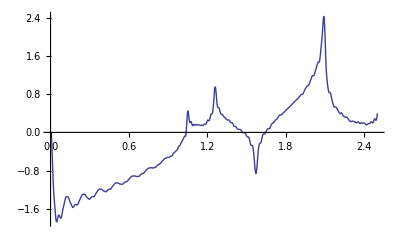

```mathematica
Plot[∑_(k=1)^50 (Sin[(6k-5)x]/(6k-5)+Sin[(5k-4)x]/(5k-4)-Sin[(4k-3)x]/(4k-3)+Sin[(3k-2) x]/(3k-2)-Sin[(2k-1) x]/(2k-1)-Sin[(k) x]/k),{x,0,2.5}]
```

```mathematica
N[∑_(k=1)^50 (Sin[(6k-5)x]/(6k-5)+Sin[(5k-4)x]/(5k-4)-Sin[(4k-3)x]/(4k-3)+Sin[(3k-2) x]/(3k-2)-Sin[(2k-1) x]/(2k-1)-Sin[(k) x]/k),100]/.x->{2.090001,2.0900002}
```

{2.42255,2.42255}